## Figure 1

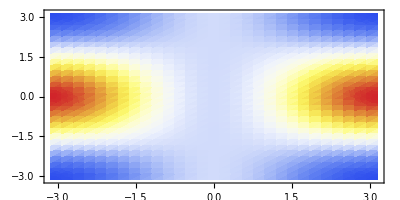

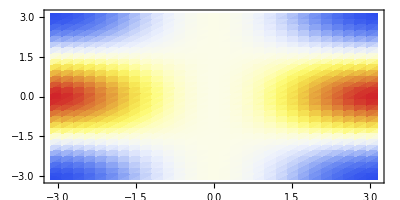

```mathematica
Clear[CRY,Id,X,Y,Z,RX,RY,RZ,ψ,HA]
{Id,X,Y,Z}=Table[PauliMatrix[i],{i,0,3}];

RX[θ_]:=MatrixExp[-I θ X/2];
RY[θ_]:=MatrixExp[-I θ X/2];
RZ[θ_]:=MatrixExp[-I θ X/2];
CRY[θ_]:={{1,0,0,0},{0,1,0,0},{0,0,Cos[θ/2],-Sin[θ/2]},{0,0,Sin[θ/2],Cos[θ/2]}};

HA=DiagonalMatrix[{1,2,3,0}];
HB=DiagonalMatrix[{1,1,2,0}];

ψ=CRY[θ2].KroneckerProduct[RX[θ1],Id].{1,0,0,0};

HAvg=Refine[Conjugate[ψ].HA.ψ,{θ1∈Reals,θ2∈Reals}]//FullSimplify;
HBvg=Refine[Conjugate[ψ].HB.ψ,{θ1∈Reals,θ2∈Reals}]//FullSimplify;

DensityPlot[HAvg,{θ1,-π,π},{θ2,-π,π},AspectRatio->1/2,ColorFunction->"TemperatureMap",PlotPoints->30]
DensityPlot[HBvg,{θ1,-π,π},{θ2,-π,π},AspectRatio->1/2,ColorFunction->"TemperatureMap",PlotPoints->30]
```